# Calcolo della risposta forzata per Sistemi LTI-TD

```mathematica
G[z_]:=(z-2)/(z^3+3/2 z^2+3/4 z+1/8)
```

Calcolo i poli del sistema

```mathematica
Solve[Denominator[G[z]]==0,z]
```

{{z→-1/2},{z→-1/2},{z→-1/2}}

Scrivo la risposta forzata in z

```mathematica
Subscript[Y, f][z_]:=G[z](z/(z-1))
```

```mathematica
Subscript[Y, f][z]
```

((-2+z) z)/((-1+z) (1/8+(3 z)/4+(3 z^2)/2+z^3))

```mathematica
Factor[(Subscript[Y, f][z])/z]
```

(8 (-2+z))/((-1+z) (1+2 z)^3)

```mathematica
Subscript[C, 1](1/(z-1))+Subscript[C, 21](1/(z+1/2))+Subscript[C, 22](1/(z+1/2)^2)+Subscript[C, 23](1/(z+1/2)^3)
```

C_1/(-1+z)+C_21/(1/2+z)+C_22/(1/2+z)^2+C_23/(1/2+z)^3

```mathematica
Subscript[C, 1]=lim_(z->1) (z-1)((Subscript[Y, f][z])/z)
```

-8/27

```mathematica
G[1]
```

-8/27

```mathematica
Subscript[C, 23]=lim_(z->-1/2) (z+1/2)^3((Subscript[Y, f][z])/z)
```

5/3

```mathematica
Subscript[C, 22]=lim_(z->-1/2) D[(z+1/2)^3((Subscript[Y, f][z])/z),z]
```

4/9

```mathematica
Subscript[C, 21]=(1/2)lim_(z->-1/2) D[D[(z+1/2)^3((Subscript[Y, f][z])/z),z],z]
```

8/27

```mathematica
Subscript[C, 1](1/(z-1))+Subscript[C, 21](1/(z+1/2))+Subscript[C, 22](1/(z+1/2)^2)+Subscript[C, 23](1/(z+1/2)^3)
```

-8/(27 (-1+z))+5/(3 (1/2+z)^3)+4/(9 (1/2+z)^2)+8/(27 (1/2+z))

Per “sistemare” i fratti semplici di Yf[z] bisogna moltiplicare per z ciascun fratto semplice

```mathematica
Subscript[C, 1](z/(z-1))+Subscript[C, 21](z/(z+1/2))+Subscript[C, 22](z/(z+1/2)^2)+Subscript[C, 23](z/(z+1/2)^3)
```

-(8 z)/(27 (-1+z))+(5 z)/(3 (1/2+z)^3)+(4 z)/(9 (1/2+z)^2)+(8 z)/(27 (1/2+z))

Scriviamo la risposta forzata nel dominio del Tempo

```mathematica
Subscript[y, f][k_]:=Subscript[C, 1] UnitStep[k]+Subscript[C, 21](-1/2)^k UnitStep[k]+Subscript[C, 22] Binomial[k,1](-1/2)^(k-1)UnitStep[k]+Subscript[C, 23] Binomial[k,2](-1/2)^(k-2)UnitStep[k]
```

```mathematica
Subscript[y, f][k]
```

-(8 UnitStep[k])/27+1/27 (-1)^k 2^(3-k) UnitStep[k]+1/9 (-1)^(-1+k) 2^(3-k) k UnitStep[k]+5/3 (-1)^(-2+k) 2^(1-k) (-1+k) k UnitStep[k]

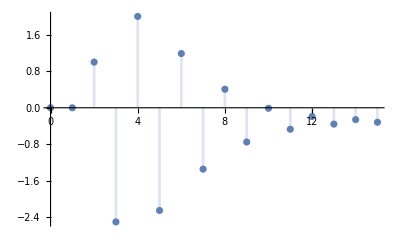

```mathematica
DiscretePlot[Subscript[y, f][k],{k,0,15},PlotRange->All]
```

Calcolo della risposta all’impulso che e’ per definizione l’antitrasformata zeta della FdT del sistema

```mathematica
G[z]
```

(-2+z)/(1/8+(3 z)/4+(3 z^2)/2+z^3)

```mathematica
Factor[G[z]/z]
```

(8 (-2+z))/(z (1+2 z)^3)

```mathematica
Apart[G[z]/z]
```

-16/z+40/(1+2 z)^3+32/(1+2 z)^2+32/(1+2 z)

```mathematica
Subscript[D, 1](1/z)+Subscript[D, 21](1/(z+1/2))+Subscript[D, 22](1/(z+1/2)^2)+Subscript[D, 23](1/(z+1/2)^3)
```

D_1/z+D_21/(1/2+z)+D_22/(1/2+z)^2+D_23/(1/2+z)^3

```mathematica
Subscript[D, 1]=lim_(z->0) z (G[z]/z)
```

-16

```mathematica
Subscript[D, 23]=lim_(z->-1/2) (z+1/2)^3(G[z]/z)
```

5

```mathematica
Subscript[D, 22]=lim_(z->-1/2) D[(z+1/2)^3(G[z]/z),z]
```

8

```mathematica
Subscript[D, 21]=(1/2)lim_(z->-1/2) D[D[(z+1/2)^3(G[z]/z),z],z]
```

16

Moltiplico tutto per z al fine di sistema l’antitrasformata ed identificare le successioni elementari

```mathematica
Subscript[D, 1]+Subscript[D, 21](z/(z+1/2))+Subscript[D, 22](z/(z+1/2)^2)+Subscript[D, 23](z/(z+1/2)^3)
```

-16+(5 z)/(1/2+z)^3+(8 z)/(1/2+z)^2+(16 z)/(1/2+z)

```mathematica
g[k_]:=Subscript[D, 1] KroneckerDelta[k]+Subscript[D, 21](-1/2)^k UnitStep[k]+Subscript[D, 22] Binomial[k,1](-1/2)^(k-1)UnitStep[k]+Subscript[D, 23] Binomial[k,2](-1/2)^(k-2)UnitStep[k]
```

```mathematica
g[k]
```

-16 k+(-1)^k 2^(4-k) UnitStep[k]+(-1)^(-1+k) 2^(4-k) k UnitStep[k]+5 (-1)^(-2+k) 2^(1-k) (-1+k) k UnitStep[k]

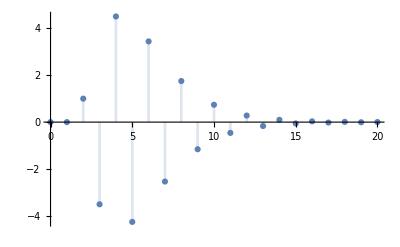

```mathematica
DiscretePlot[g[k],{k,0,20},PlotRange->All]
```